```mathematica
a=Table[{},{i,3}]
```

{{},{},{}}

```mathematica
a[[1]]=={}
```

True

```mathematica
Dimensions[Table[1,{i,4},{j,4}]]
```

{4,4}

```mathematica
{dimN,dimM}=Dimensions[img];
```

```mathematica
dimN
```

21

```mathematica
dimM
```

21

```mathematica
imgZ[[5;;6,20;;21]]
```

{{-0.593893,-0.3},{-0.609017,-0.3}}

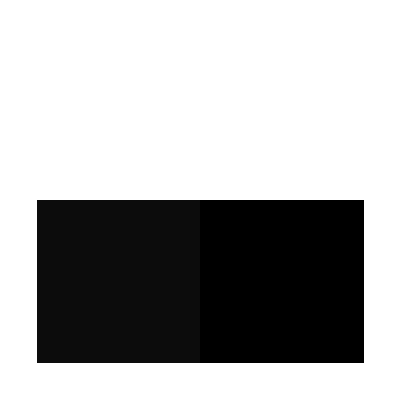

```mathematica
showGrayImage[imgZ[[5;;6,20;;21]]]
```

```mathematica
imgZ=extractZeroContour2D[imgSyn,.3];
```

```mathematica
imgSyn;
```

```mathematica
bigEdgeUsageTable[dimN,dimM];
```

```mathematica
Dimensions[cycles]
```

{256}

```mathematica
a=cycles[[FromDigits[{1,0,1,0,0,0,0,0},2]+1]]
```

{{{1,2},{1,5},{3,7},{3,4}}}

```mathematica
a⟦1,1⟧
```

{1,2}

```mathematica
Length[a⟦1,1⟧]
```

2

```mathematica
Length[a⟦1⟧]
```

4

```mathematica
a[[1,1]]=={1,2}
```

True

```mathematica
contour2D[img_,iso_]:=Module[{imgZeroOut,dataTable,dimN,dimM,config,imgEdgeCoor1,imgEdgeCoor2,v1,v2,myPolyV,myPolyVIndex,myEdge,myPolyE,myPolyEIndex,myPoly},
(*initialize empty vertices and edges' set;initialize v1,v2*)
myPolyV={};myPolyE={};v1=0;v2=0;
myPolyVIndex=1;
myPolyEIndex=1;
(*get the dimension of the image*)
 {dimN,dimM}=Dimensions[img];

Do[
(*get the configuration for this 2 by 2 pixel grid*)
config=configTable2D[twoBytwoMap[imgZeroOut⟦i,j+1⟧,imgZeroOut⟦i+1,j+1⟧,imgZeroOut⟦i,j⟧,imgZeroOut⟦i+1,j⟧]];

Do[
(*loop thru the edges that we are going to to build up one at a time*)
imgEdgeCoor1=getEdgeCoorByNumber[config⟦k,1⟧,i,j];
imgEdgeCoor2=getEdgeCoorByNumber[config⟦k,2⟧,i,j];
(*
Print["At ",i ,", ",j];*)

v1=If[dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myPolyV=Append[myPolyV,interpolate[config⟦k,1⟧,i,j,imgZeroOut]];
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧=myPolyVIndex;
myPolyVIndex++;
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧];

v2=If[dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧≠0,dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧,
myPolyV=Append[myPolyV,interpolate[config⟦k,2⟧,i,j,imgZeroOut]];
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧=myPolyVIndex;
myPolyVIndex++;
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧];

(*push the edge into the edge set*)
myEdge={v1,v2};
myPolyE=Append[myPolyE,myEdge];
myPolyEIndex++;
,{k,Length[config]}];

,{i,dimN-1},{j,dimM-1}];
myPoly={myPolyV,myPolyE};
myPoly
]
```

```mathematica
Dimensions[volSyn]
```

{11,11,11}

```mathematica
bigEdgeUsageTable3D[11,11,11]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},17,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},21,{1}}
 |  |  |  |

```mathematica
volSyn
```

{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.531657,-0.860239,-0.860239,-0.531657,0.,0.531657,0.860239,0.860239,0.531657,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.531657,0.860239,0.860239,0.531657,0.,-0.531657,-0.860239,-0.860239,-0.531657,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.328582,-0.531657,-0.531657,-0.328582,0.,0.328582,0.531657,0.531657,0.328582,0.},{0.,-0.203075,-0.328582,-0.328582,-0.203075,0.,0.203075,0.328582,0.328582,0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.328582,0.531657,0.531657,0.328582,0.,-0.328582,-0.531657,-0.531657,-0.328582,0.},{0.,0.203075,0.328582,0.328582,0.203075,0.,-0.203075,-0.328582,-0.328582,-0.203075,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
imgZeroOut=extractZeroContour3D[volSyn,.3];
```

```mathematica
makeConfigList[imgZeroOut,1,1,1]
```

{0,0,0,0,0,0,0,0}

```mathematica
FromDigits[{1,1,1,1,1,1,1,1},2]+1
```

256

```mathematica
FromDigits["10000010",2]
```

130

```mathematica
cycles⟦1⟧
```

{}

```mathematica
imgEdgeCoor1=getEdgeCoorByNumber3D[config⟦q,1⟧,i,j,k];
imgEdgeCoor2=getEdgeCoorByNumber3D[config⟦q,2⟧,i,j,k];
imgEdgeCoor3=getEdgeCoorByNumber3D[config⟦q,3⟧,i,j,k];
(*
Print[imgEdgeCoor1];*)
(*for each point which we are about to calculate*)
v1=If[dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧,imgEdgeCoor1⟦3⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧,imgEdgeCoor1⟦3⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myMeshV=Append[myMeshV,interpolate3D[config⟦q,1⟧,i,j,k,imgZeroOut]];
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧,imgEdgeCoor1⟦3⟧⟧=myMeshVIndex;
myMeshVIndex++;
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧,imgEdgeCoor1⟦3⟧⟧];

v2=If[dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧,imgEdgeCoor2⟦3⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧,imgEdgeCoor2⟦3⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myMeshV=Append[myMeshV,interpolate3D[config⟦q,2⟧,i,j,k,imgZeroOut]];
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧,imgEdgeCoor2⟦3⟧⟧=myMeshVIndex;
myMeshVIndex++;
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧,imgEdgeCoor2⟦3⟧⟧];

v3=If[dataTable⟦imgEdgeCoor3⟦1⟧,imgEdgeCoor3⟦2⟧,imgEdgeCoor3⟦3⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor3⟦1⟧,imgEdgeCoor3⟦2⟧,imgEdgeCoor3⟦3⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myMeshV=Append[myMeshV,interpolate3D[config⟦q,3⟧,i,j,k,imgZeroOut]];
dataTable⟦imgEdgeCoor3⟦1⟧,imgEdgeCoor3⟦2⟧,imgEdgeCoor3⟦3⟧⟧=myMeshVIndex;
myMeshVIndex++;
dataTable⟦imgEdgeCoor3⟦1⟧,imgEdgeCoor3⟦2⟧,imgEdgeCoor3⟦3⟧⟧];
```

```mathematica
{1,2,3}⟦1;;2⟧
```

{1,2}